```mathematica
temperature=Table[i,{i,10,500,10}];
temperature=Delete[temperature,5];
dimension = 2;
```

```mathematica
Optdissipation=
Table[
Print["Constructing "<>ToString[T1]<>"."];
Table[
dt=0.05;
x=Import[NotebookDirectory[]<>"../../data/LangevinData/BeadsPos_"<>ToString[dimension]<>"_"<>ToString[T1]<>"_1200_"<>ToString[j] <>".mat"][[1]];
x=Transpose[x];
L=Length[x];
x=Transpose[x];

sections=120;
NGaussian=L/sections;
hGaussian=
Table[
StandardDeviation[Transpose[x][[i;;i+sections-1]]],
{i,1,L,sections}
];
hGaussian=Join[hGaussian,hGaussian];

fGpoints=
Table[
Mean[Transpose[x][[i;;i+sections-1]]],
{i,1,L,sections}
];
fGpoints=Join[fGpoints,-fGpoints];

dGenerator=Compile[{{x1,_Real},{x2,_Real}},
Exp[-(x1-Transpose[fGpoints][[1]])^2/(Transpose[hGaussian][[1]]^2/2)]*Exp[-(x2-Transpose[fGpoints][[2]])^2/(Transpose[hGaussian][[2]]^2/2)]
];

a1=RandomReal[{-1,1},{NGaussian}];
a1=Join[a1,-a1];
a2=RandomReal[{-1,1},{NGaussian}];
a2=Join[a2,-a2];

delta=Transpose[Differences[Transpose[x]]];
xtail=Transpose[Delete[Transpose[x],-1]];
xhead=Transpose[Delete[Transpose[x],1]];
pos=(xtail+xhead)/2;

dvalue=Table[dGenerator[pos[[1,i]],pos[[2,i]]],{i,1,L-1}];
deltaJd=Total[{dvalue.a1,dvalue.a2}*delta];

CurFluc=Accumulate[deltaJd];

Tobs=20;
thermoΔJd=Table[CurFluc[[i]] - CurFluc[[i-Tobs/dt]],{i,( 1+Tobs)/dt, L-1,1/dt}];
Subscript[μ, 1]=Chop[Mean[thermoΔJd]/Tobs];
Subscript[var, 1] =Tobs Variance[thermoΔJd/Tobs]; 
Σold=2 Subscript[μ, 1]^2/Subscript[var, 1];

acceptances = 0;
trials = 5000;
β = 5000; (* Bigger β prefers the optimal d *)

  Table[

Clear[perturb1,perturb2];
perturb1=RandomReal[{-1,1},{NGaussian}];
perturb1=Join[perturb1,-perturb1];
perturb2=RandomReal[{-1,1},{NGaussian}];
perturb2=Join[perturb2,-perturb2];

newa1=a1+perturb1;
newa2=a2+perturb2;

deltaJd=Total[{dvalue.newa1,dvalue.newa2}*delta];
CurFluc=Accumulate[deltaJd];

thermoΔJd=Table[CurFluc[[i]] - CurFluc[[i-Tobs/dt]],{i,( 1+Tobs)/dt, L-1,1/dt}];
Subscript[μ, 1]=Chop[Mean[thermoΔJd]/Tobs];
Subscript[var, 1] =Tobs Variance[thermoΔJd/Tobs]; 
Σ=2 Subscript[μ, 1]^2/Subscript[var, 1];

Δenergy =β (Σold - Σ);
If[RandomReal[] <Exp[-Δenergy], 
a1=newa1;
a2=newa2;
 acceptances+=1;
Σold = Σ
];
,{trialNumber, 1, trials}
]; 
Σold
,{j,1,10}]
,{T1,temperature}]
```

Constructing 10.

Constructing 20.

Constructing 30.

Constructing 40.

Constructing 60.

Constructing 70.

Constructing 80.

Constructing 90.

Constructing 100.

Constructing 110.

Constructing 120.

Constructing 130.

Constructing 140.

Constructing 150.

Constructing 160.

Constructing 170.

Constructing 180.

Constructing 190.

Constructing 200.

Constructing 210.

Constructing 220.

Constructing 230.

Constructing 240.

Constructing 250.

Constructing 260.

Constructing 270.

Constructing 280.

Constructing 290.

Constructing 300.

Constructing 310.

Constructing 320.

Constructing 330.

Constructing 340.

Constructing 350.

Constructing 360.

Constructing 370.

Constructing 380.

Constructing 390.

Constructing 400.

Constructing 410.

Constructing 420.

Constructing 430.

Constructing 440.

Constructing 450.

Constructing 460.

Constructing 470.

Constructing 480.

Constructing 490.

Constructing 500.

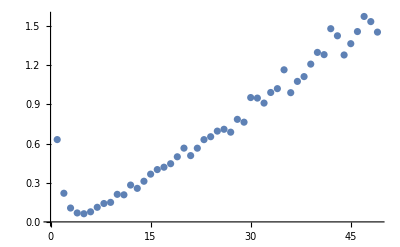

```mathematica
ListPlot[Mean[Transpose[Optdissipation]]]
```

```mathematica
Export[NotebookDirectory[]<>"../../data/OptimizedLowerBound.mat",Optdissipation];
```